## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";
```

```mathematica
Directory[]
```

/Users/chengling

## p0=3.80, N= 4096

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
Tlist={0.08868 ,0.05586 ,0.03756, 0.02652, 0.01945 ,0.01471, 0.01141};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.08868000,0.05586000,0.03756000,0.02652000,0.01945000,0.01471000,0.01141000}

```mathematica
wtlist={0.0,0.1,0.31,1.,3.16,10.,31.62,100.,316.22,1000.,3162.27}
```

{0.,0.1,0.31,1.,3.16,10.,31.62,100.,316.22,1000.,3162.27}

```mathematica
wtliststring=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@wtlist
```

{0.000000,0.100000,0.310000,1.000000,3.160000,10.000000,31.620000,100.000000,316.220000,1000.000000,3162.270000}

```mathematica
test=Import["/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/ove","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[<90,8192>, Real64],/postion→NumericArray[<90,8192>, Real64],/time→NumericArray[…],/type→NumericArray[<90,4096>, Integer32],/velocity→NumericArray[<90,8192>, Real64]|>

### Test if waiting time actually works

```mathematica
timeWT=Table[Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8000_T",Tstring[[i]],"_waitingTime",wtliststring[[wt]],"_idx0.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,Length[wtlist]}],{i,Length[Tstring]}];
```

```mathematica
overlapCRSSIFWT=Table[Table[Import[StringJoin[saveFolder,"overlapCRSISF_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",wtliststring[[wt]],"_idx0.nc"],"Data"],{wt,Length[wtlist]}],{T,Length[Tlist]}];
```

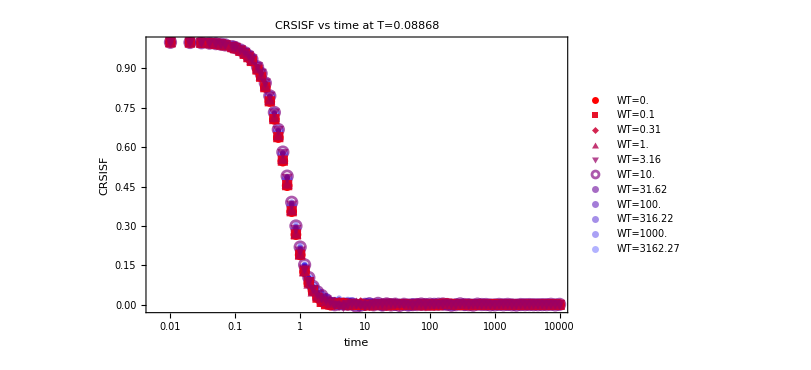

```mathematica
ListLogLinearPlot[Table[Table[{timeWT[[1,wt,rec]],Normal[overlapCRSSIFWT[[1,wt,2]]][[rec]]},{rec,Length[timeWT[[1,wt]]]}],{wt,1,11}],PlotLegends->Table["WT="<>ToString[wtlist[[wt]]],{wt,1,11}],PlotStyle->redBluePlotConfig[11],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time at T="<>ToString[Tlist[[1]]],PlotMarkers->Automatic]
```

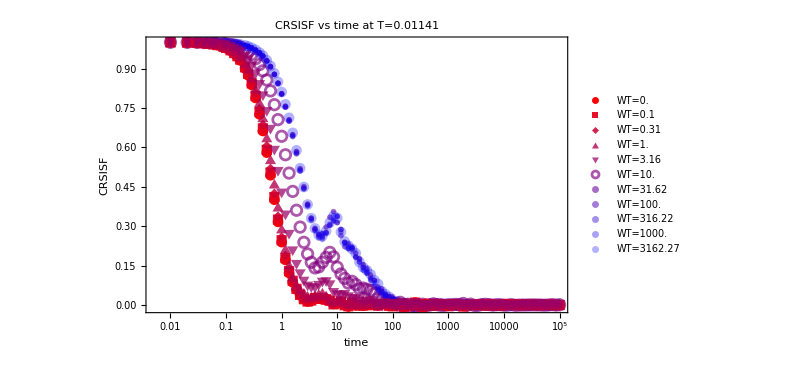

```mathematica
ListLogLinearPlot[Table[Table[{timeWT[[7,wt,rec]],Normal[overlapCRSSIFWT[[7,wt,2]]][[rec]]},{rec,Length[timeWT[[7,wt]]]}],{wt,1,11}],PlotLegends->Table["WT="<>ToString[wtlist[[wt]]],{wt,1,11}],PlotStyle->redBluePlotConfig[11],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time at T="<>ToString[Tlist[[7]]],PlotMarkers->Automatic]
```

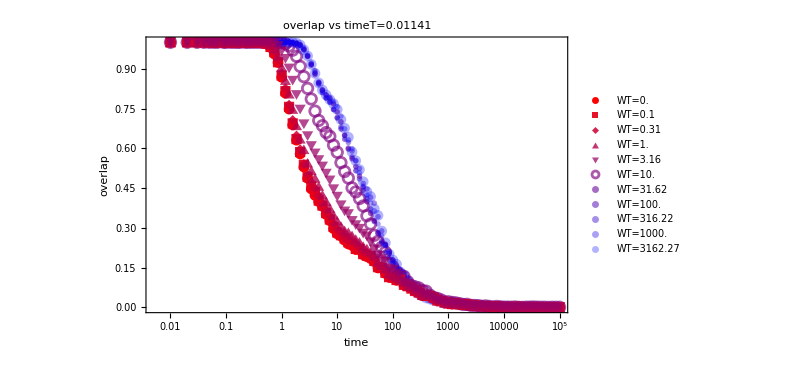

```mathematica
ListLogLinearPlot[Table[Table[{timeWT[[7,wt,rec]],Normal[overlapCRSSIFWT[[7,wt,1]]][[rec]]},{rec,Length[timeWT[[7,wt]]]}],{wt,1,11}],PlotLegends->Table["WT="<>ToString[wtlist[[wt]]],{wt,1,11}],PlotStyle->redBluePlotConfig[11],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs timeT="<>ToString[Tlist[[7]]],PlotMarkers->Automatic]
```

### τα

```mathematica
longestWT={10000.,10000.,10000.,10000.,10000.,31622.77,100000.}
```

{10000.,10000.,10000.,10000.,10000.,31622.8,100000.}

```mathematica
longestWTstring=ToString[NumberForm[#,{9,6},ExponentFunction->(Null&)]]&/@longestWT
```

{10000.000000,10000.000000,10000.000000,10000.000000,10000.000000,31622.770000,100000.000000}

```mathematica
overlapCRSSIF=Table[Table[Import[StringJoin[saveFolder,"overlapCRSISF_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",longestWTstring[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
time=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8000_T",Tstring[[T]],"_waitingTime",longestWTstring[[T]],"_idx0.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{T,Length[Tstring]}];
```

```mathematica
overlap=Table[Table[Mean[Table[Normal[overlapCRSSIF[[T,i,1,rec]]],{i,3}]],{rec,Length[overlapCRSSIF[[T,1,1]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISF=Table[Table[Mean[Table[Normal[overlapCRSSIF[[T,i,2,rec]]],{i,3}]],{rec,Length[overlapCRSSIF[[T,1,2]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISF[[1,1]]
```

1.

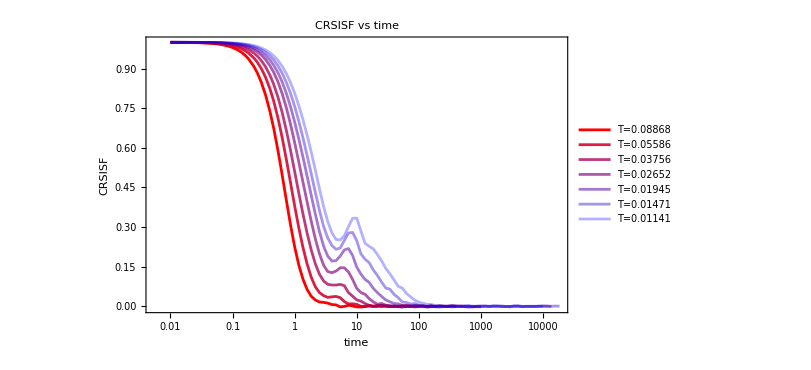

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],CRSISF[[T,rec]]},{rec,Length[CRSISF[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

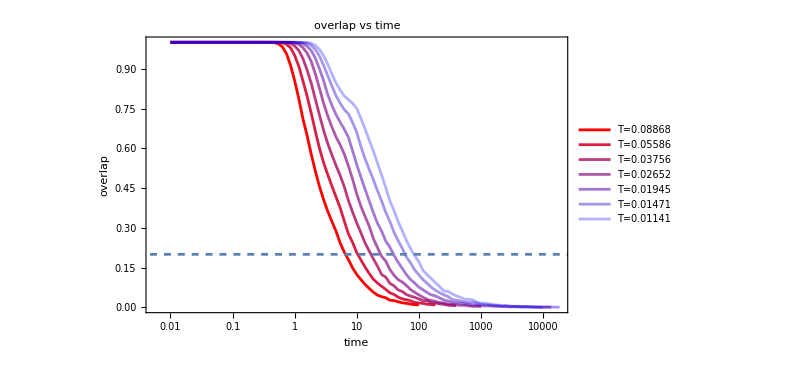

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[T,rec]],overlap[[T,rec]]},{rec,Length[CRSISF[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True];
Show[CRSISFPlot,LogLinearPlot[0.2,{x,0.001,100000},PlotStyle->Dashed]]
```

```mathematica
overlapCRSSIF[[1,1,1,1]]
```

1.

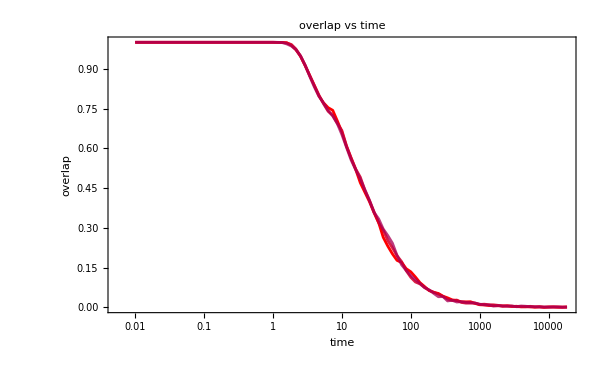

```mathematica
ListLogLinearPlot[Table[Table[{time[[6,rec]],overlapCRSSIF[[6,i,1,rec]]},{rec,Length[CRSISF[[6]]]}],{i,3}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
TauAol={6.656916336382439,
10.532655112230382,
17.261092293760527,
25.00279850043277,
40.26115307072112,
61.488680836669154,
85.97848233539733}
```

{6.65692,10.5327,17.2611,25.0028,40.2612,61.4887,85.9785}

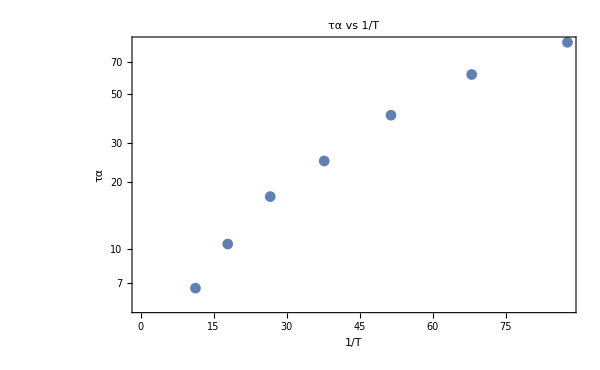

```mathematica
ListLogPlot[Table[{1/Tlist[[T]],TauAol[[T]]},{T,Length[Tlist]}],FrameLabel->{"1/T","τα"},ImageSize->600,PlotLabel->"τα vs 1/T"]
```

```mathematica
fitting=NonlinearModelFit[Table[{1/Tlist[[T]],TauAol[[T]]},{T,Length[Tlist]}],A*x^B,{A,B},x]
```

FittedModel[0.177174 x^1.38267]

```mathematica
fitting[[1]]
```

{Nonlinear,{A→0.177174,B→1.38267},{{x},A x^B}}

```mathematica
Table[Solve[fitting[1/T]==10^(1/3*i),T][[1,1]],{i,3,12}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{T→0.0540977,T→0.0310528,T→0.0178247,T→0.0102316,T→0.00587305,T→0.0033712,T→0.00193511,T→0.00111078,T→0.0006376,T→0.00036599}

```mathematica
time[[7,40]]
```

10.

```mathematica
Length[timeNVT[[1,1]]]
```

35

```mathematica
timeCRSISFDifferentN=Table[Table[Table[{timeNVT[[i,1,rec]],CRSISFDifferentN[[i,n,rec]]},{rec,20,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],{n,3}];
```

```mathematica
fit=NonlinearModelFit[timeCRSISFDifferentN[[2]][[1]],{stretchedExp[t,G,τ,β],{1>β>0.01,0<G<1,τ>0}},{G,τ,β},t];
```

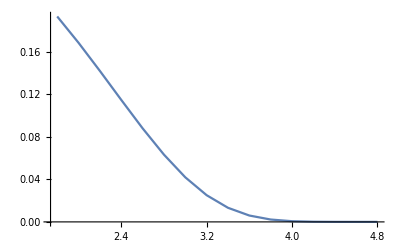

```mathematica
fitPlot=ListLinePlot[Table[{Log10[timeNVT[[1,1,rec]]+0.01],SISFfitsDifferentN[[1]][[3]][timeNVT[[1,1,rec]]]},{rec,20,Length[CRSISFDifferentN[[1,1]]]}]]
```

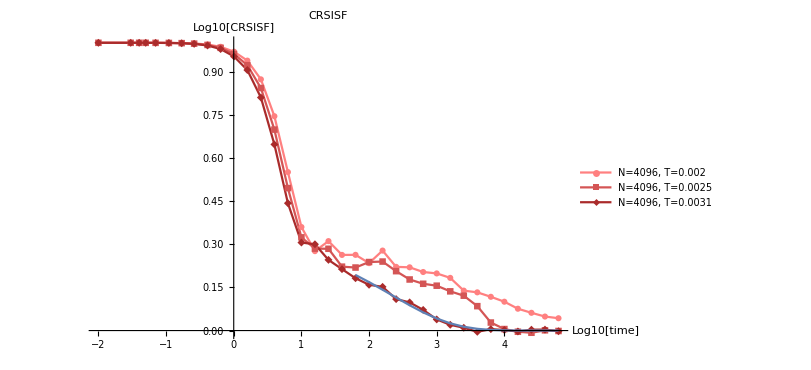

```mathematica
Show[CRSISFPlot,fitPlot]
```

```mathematica
SISFfitsDifferentN[[3]][[1]]["BestFitParameters"]
```

{G→0.999445,τ→10.737,β→0.255685}

```mathematica
Simplify[Log10[A Exp[(-b)^c]]]
```

Log[A ⅇ^((-b)^c)]/Log[10]

```mathematica
timeCRSISFDifferentN[[3]][[3]]
```

{{63.1,0.423591},{100.,0.389313},{158.49,0.347963},{251.19,0.339029},{398.11,0.297434},{630.96,0.257363},{1000.,0.208064},{1584.89,0.133766},{2511.89,0.070347},{3981.07,0.0189599},{6309.57,0.00486076},{10000.,-0.00477611},{15848.9,-0.00480651},{25118.9,-0.00689134},{39810.7,-0.00250884},{63095.7,-0.0016598}}

```mathematica
fitsDifferentN=Table[Table[NonlinearModelFit[timeCRSISFDifferentN[[n]][[T]],{stretchedExp[t,G,τ,β],{1>β>0.01,0<G<1,τ>0}},{G,τ,β},t],{T,3}],{n,3}];
```

```mathematica
SISFfitsDifferentN=Table[Table[NonlinearModelFit[timeSISFDifferentN[[n]][[T]],{stretchedExp[t,G,τ,β],{1>β>0.01,0<G<1,τ>0}},{G,τ,β},t],{T,3}],{n,3}];
```

```mathematica
τCRSISFDN=Table[Table[fitsDifferentN[[n]][[T]]["BestFitParameters"][[2,2]],{T,3}],{n,3}]
```

{{23004.5,5409.22,1843.04},{9566.57,4227.21,1551.34},{4987.84,2078.03,1287.55}}

```mathematica
τSISFDN=Table[Table[SISFfitsDifferentN[[n]][[T]]["BestFitParameters"][[2,2]],{T,3}],{n,3}]
```

{{4419.22,2701.88,213.739},{229.291,935.641,308.564},{13.067,267.384,8.02368}}

```mathematica
Grid[τCRSISFDN]
```

23004.5 | 5409.22 | 1843.04
9566.57 | 4227.21 | 1551.34
4987.84 | 2078.03 | 1287.55

## τ from overlapfunction

```mathematica
overlapN=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[n]]],"/nvt_Overlap_N",ToString[Ns[[n]]],"_p3.800_T",TstringNVT[[i]],"_0.csv"],"CSV"][[1]],{n,3}],{i,Length[TstringNVT]}];
```

```mathematica
ovelap512=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[1]]],"/nvt_Overlap_N",ToString[Ns[[1]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,9}],{i,Length[TstringNVT]}];
```

```mathematica
overlap512Mean=Table[Table[Mean[Table[ovelap512[[i,idx]][[time]],{idx,10}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
ovelap1024=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/AnalyticalG/data/N",ToString[Ns[[2]]],"/nvt_Overlap_N",ToString[Ns[[2]]],"_p3.800_T",TstringNVT[[i]],"_",ToString[idx],".csv"],"CSV"][[1]],{idx,0,2}],{i,Length[TstringNVT]}];
```

```mathematica
overlap1024Mean=Table[Table[Mean[Table[ovelap1024[[i,idx]][[time]],{idx,3}]],{time,Length[timeNVT[[i,1]]]}],{i,Length[timeNVT]}];
```

```mathematica
timeOverlapDifferentN={Table[Table[{timeNVT[[i,1,rec]],overlap512Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],overlap1024Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],Table[Table[{timeNVT[[i,1,rec]],overlapN[[i,3,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}]};
```

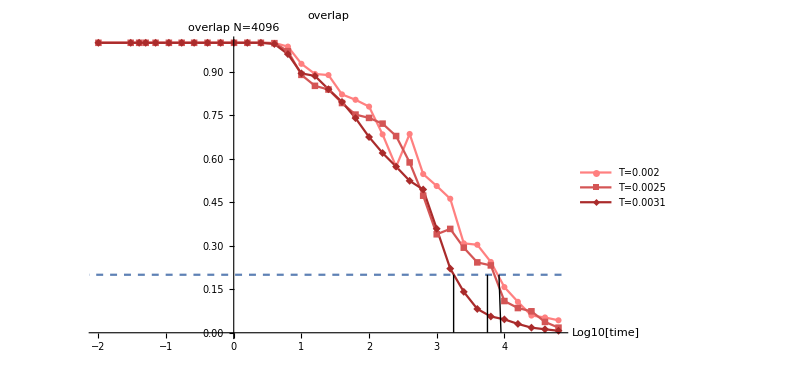

```mathematica
Show[ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],overlapN[[i,3,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","overlap N=4096"},ImageSize->600,PlotLabel->"overlap",PlotRange->Automatic],Plot[0.2,{x,-10,100},PlotStyle->Dashed],Graphics[Line[{{3.25,0},{3.25,0.2}}]],Graphics[Line[{{3.75,0},{3.75,0.2}}]],Graphics[Line[{{3.95,0},{3.92,0.2}}]]]
```

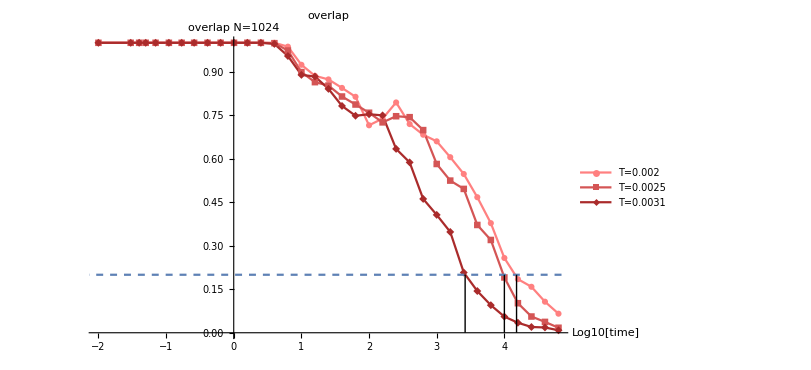

```mathematica
Show[ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],overlap1024Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","overlap N=1024"},ImageSize->600,PlotLabel->"overlap",PlotRange->Automatic],Plot[0.2,{x,-10,100},PlotStyle->Dashed],Graphics[Line[{{3.42,0},{3.42,0.2}}]],Graphics[Line[{{4.0,0},{4.0,0.2}}]],Graphics[Line[{{4.18,0},{4.18,0.2}}]]]
```

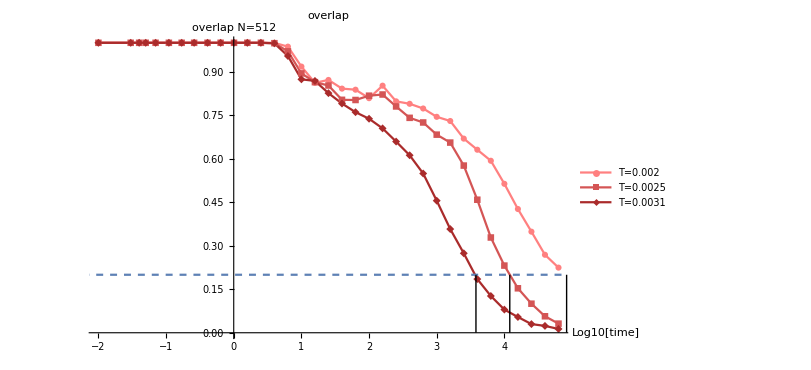

```mathematica
Show[ListLinePlot[Table[Table[{Log10[timeNVT[[i,1,rec]]+0.01],overlap512Mean[[i,rec]]},{rec,Length[CRSISFDifferentN[[i,1]]]}],{i,Length[timeNVT]}],
PlotStyle->Table[Blend[{GrayLevel[1-i/Length[timeNVT]],RGBColor[1,0,0]},0.5],{i,0,Length[timeNVT]}],PlotMarkers->Automatic,PlotLegends->Table[StringJoin["T=",ToString[TlistNVT[[i]]]],{i,Length[timeNVT]}],AxesLabel->{"Log10[time]","overlap N=512"},ImageSize->600,PlotLabel->"overlap",PlotRange->
Automatic],Plot[0.2,{x,-10,100},PlotStyle->Dashed],Graphics[Line[{{3.58,0},{3.58,0.2}}]],Graphics[Line[{{4.08,0},{4.08,0.2}}]],Graphics[Line[{{4.92,0},{4.92,0.2}}]]]
```

```mathematica
ex10[x_]:=10^x;
```

```mathematica
τoverlapDN=ex10/@{{4.92,4.08,3.58},{4.18,4.0,3.42},{3.95,3.75,3.25}}
```

{{83176.4,12022.6,3801.89},{15135.6,10000.,2630.27},{8912.51,5623.41,1778.28}}